```mathematica
Quit[]
```

```mathematica
<<"Turtle`"
```

```mathematica
Graphics[{
ParseDirectives[{
"echo"["Dashed"],{"forward"[0.25],"Text"[Style["q",Large],{0,1}]},"Forward"[.5],"echo"["Dashing[None]"],(* Horizontal dashed line *)
{
"turn"[30°],
{"forward"[1],"Arrow"[]}, (* Arrow *)
{"forward"[1.2],"mark"["A"]}, (* Mark point A *)
"Forward"[2],(* Upper solid line *)
"Text"[Style["p_1",Large],{-1,1}]
},
{
"turn"[-30°],
{"forward"[1],"turn"[180°],"Arrow"[]}, (* Arrow *)
{
"forward"[1.2],"on"["Wavy"],{"goto"["A",0.5],"Text"[Style["p-k",Large],{-2,0}]},"Goto"["A",1],"off"["Wavy"]}, (* Vertical dashed line *)
"Forward"[2], (* Lower solid line *)
"Text"[Style["p_2",Large],{-1,-1}]
}
},WavyStyle->{0.3,0.08}]
},PlotRange->{{0,2.5},{-1.25,1.25}}]
```

-Graphics-

```mathematica
Graphics[{
ParseDirectives[{
"on"["Wavy"],"Forward"[1],"turn"[90°],"Forward"[1],"Arrow"[]
},WavyStyle->{0.03,0.03}]
}]
```

-Graphics-

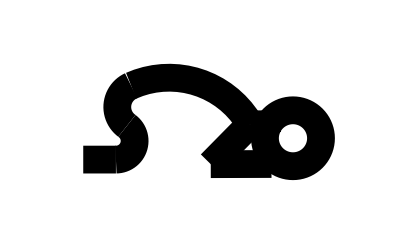

```mathematica
Graphics[{
Thickness[0.05],
ParseDirectives[{
"Forward"[0.7],
"Bend"[(4π)/5,0.4],
"Bend"[-4/6 π,0.5],
"Bend"[-1.4/3 π,2],
{
"turn"[-1.3],
"Forward"[1.2],
"turn"[2.35],
"Forward"[1.3]
},
{
"turn"[(1π)/3],
"Forward"[0.4],
"turn"[π/3],
"Bend"[-2π,0.6]
}
}]
},PlotRange->{{-1,6},{-1,3}}]
```